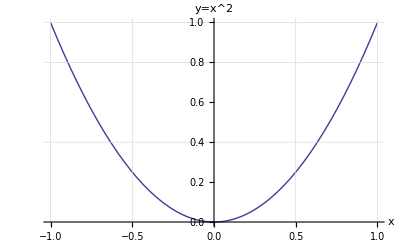

```mathematica
Plot[x^2,{x,-1,1},AxesLabel->{"x","y=x^2"},GridLines->{{0.5,1,-0.5,-1},{0.4,1,0.8}}]
```

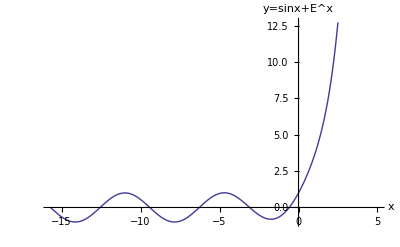

```mathematica
Plot[E^x+Sin[x],{x,-5π,5},AxesLabel->{"x","y=sinx+E^x"},GridLines->{{π,2π,3π,-π,-2π,-3π,-4π,-5π},{-1,1,2,3,4}}]
```

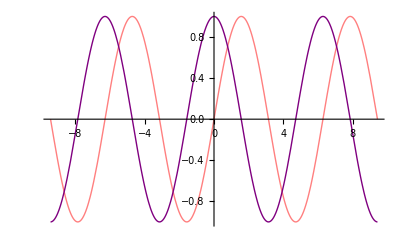

```mathematica
Plot[{Sin[x],Cos[x]},{x,-3π,3π},PlotStyle->{Pink,Purple}]
```

```mathematica
<<"PlotLegends`"
```

```mathematica
Plot[{Sin[x],Cos[x]},{x,-3π,3π},PlotStyle->{Pink,Purple},PlotLegend->{"y=Sinx","y=Cosx"}]
```

-Graphics-

```mathematica
Plot[{Sin[x],Cos[x]},{x,-3π,3π},PlotStyle->{Pink,Purple},PlotLegend->{"y=Sinx","y=Cosx"},LegendPosition->{1,0}]
```

-Graphics-

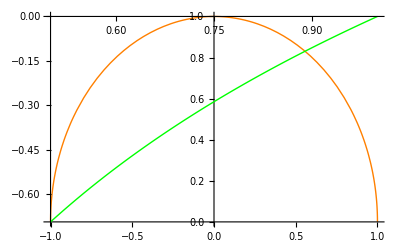

```mathematica
Show[{Plot[√(1-x^2),{x,-1,1},PlotStyle->{Orange},PlotLegend->{"y=√(1 - x^2)"},LegendPosition->{1,0.3}],Plot[Log[x],{x,0.5,1},PlotStyle->{Green},PlotLegend->{"y=lnx"},LegendPosition->{1,0}]}]
```

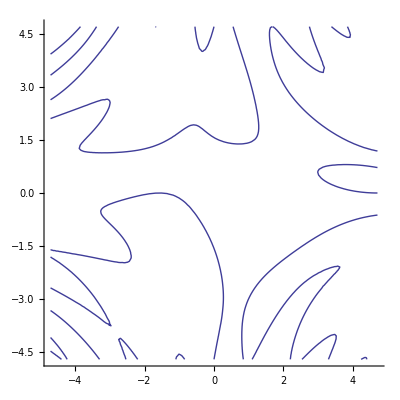

```mathematica
ContourPlot[Sin[x*y]==Sin[x]+Cos[y],{x,-3π/2,3π/2},{y,-3π/2,3π/2},Axes->True,Frame->False,AxesLabel->{"x"'"y"}]
```

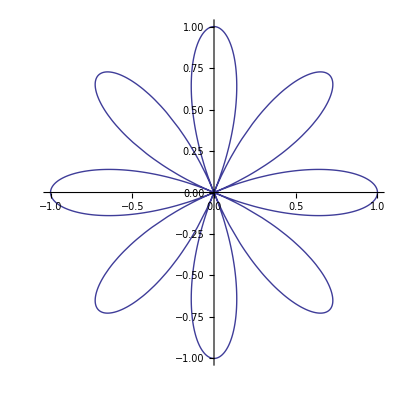

```mathematica
PolarPlot[Cos[4θ],{θ,0,2π}]
```

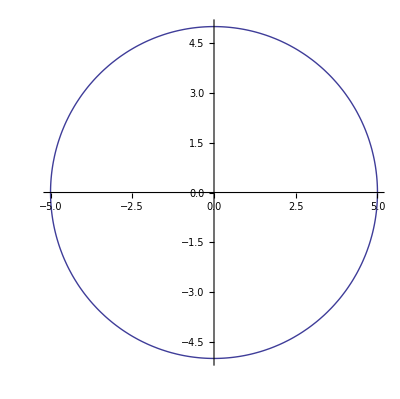

```mathematica
ParametricPlot[{5Cos[θ],5Sin[θ]},{θ,0,2π}]
```